```mathematica
dat=Get["/Users/jony/Documents/Work/Computing/ProjectX/Projects/algebolic/nb/data/spea-animation-data2.txt"];
```

```mathematica
plotPareto[dat_]:=With[{pr={{15,80},{0,5}}},
Show[
ListLogPlot[dat,PlotStyle->{{Opacity[0.6],Blue},{Opacity[1],PointSize[0.03],Red}},PlotRange->pr,Axes->False],
ListLogPlot[Sort[Last[dat]],Joined->True,InterpolationOrder->0,PlotRange->All,Axes->False],
PlotRange->pr,Frame->True]]
```

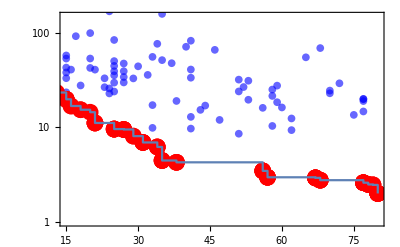

```mathematica
plotPareto[dat⟦1500⟧]
```

```mathematica
pl=plotPareto/@dat;
```

```mathematica
ListAnimate[pl,15]
```